SUPPLEMENTARY MATERIAL

1. Plots a single trajectory from our resource dynamics cognitive model

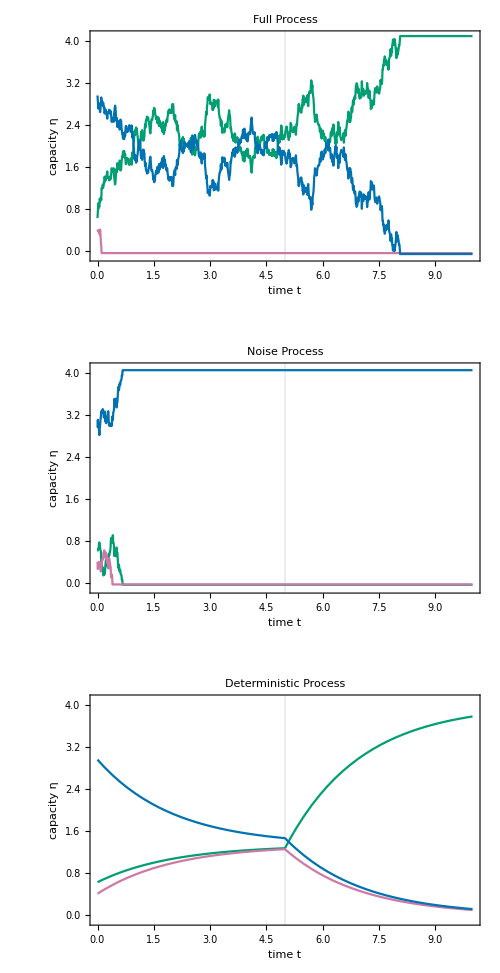

```mathematica
ClearAll["Global`*"]

(* single resource allocation trajectory plotter *)

plotter[η_,κ_,m_,q_,tq_,tmax_,Δt_:0.01]:=Block[{xopt0,xopt1,x0,xs,xts,B,M,Σ,μ,proc,procstoc,outX,outXstoc,procdet,outXdet,t,κin,TrendColors},

SeedRandom[RandomInteger[9999]];

(* defines variables and initial condition *)
x0=Map[η*Join[#,{1-Total[#]}]&,RandomVariate[DirichletDistribution[ConstantArray[1,{m}]],1]][[1]];
xs=Table[Symbol["x"<>ToString[i]],{i,m}];
xts=Map[(#[t]&),xs];

(* control set-point before and after cue *)
xopt0=ConstantArray[η/m,{m}];
xopt1=Clip[If[q<1.00,Prepend[ConstantArray[η/m-(1/m) Log[(m-1) q/(1-q)],{m-1}],η/m+((m-1)/m) Log[(m-1) q/(1-q)]],Prepend[ConstantArray[0,{m-1}],η]],{0,η}];


(* drift and diffusion matrices *)
B[x_]:=DiagonalMatrix[Map[Boole[#>0]&,x]];
M[x_]:=Total[Map[Boole[#>0]&,x]];
Σ=B[xts].(IdentityMatrix[m]-1/M[xts] ConstantArray[1,{m,m}].B[xts]);
μ[xoptin_,κin_]:=Σ.(κin (xoptin-xts));


(* full process *)
proc[x0in_]:=Block[{X0,X1},X0=RandomFunction[ItoProcess[{μ[xopt0,κ],Σ},{xs,x0in},{t,0.}],{0.,tq,Δt}];
X1=RandomFunction[ItoProcess[{μ[xopt1,κ],Σ},{xs,X0["LastValues"][[1]]},{t,0.}],{tq,tmax,Δt}];
TimeSeriesInsert[X0,X1]];
outX=proc[x0];

(* noise/diffusion process *)
procstoc[x0in_]:=Block[{X0,X1},X0=RandomFunction[ItoProcess[{μ[xopt0,0.0],Σ},{xs,x0in},{t,0.}],{0.,tq,Δt}];
X1=RandomFunction[ItoProcess[{μ[xopt1,0.0],Σ},{xs,X0["LastValues"][[1]]},{t,0.}],{tq,tmax,Δt}];
TimeSeriesInsert[X0,X1]];
outXstoc=procstoc[x0];

(* deterministic/drift process *)
procdet[x0in_]:=Block[{X0,X1},X0=NDSolveValue[{D[xts,t]==μ[xopt0,κ],(xts/. t->0)==x0in},xts,{t,0,tq}];
X1=NDSolveValue[{D[xts,t]==μ[xopt1,κ],((xts==X0)/. t->tq)},xts,{t,tq,tmax}];
Table[Piecewise[{{X0[[i]],t<tq},{X1[[i]],True}}],{i,m}]];
outXdet=procdet[x0];

(* plotting *)
TrendColors=RGBColor/@{"#009E73","#CC79A7","#0072B2"};
GraphicsColumn[{

ListLinePlot[outX,PlotStyle->Take[TrendColors,m],PlotTheme->"Scientific",PlotRange->{{0.,tmax},{-0.10,η+.10}},AspectRatio->1/GoldenRatio,PlotRangePadding->0,FrameStyle->Black,FrameLabel->{Style["time t",12],Style["capacity η",12]},GridLines->{{tq},{}},PlotLabel->Style["Full Process",12,Bold,Black],ImageSize->Full],

ListLinePlot[outXstoc,PlotStyle->Take[TrendColors,m],PlotTheme->"Scientific",PlotRange->{{0.,tmax},{-0.10,η+.10}},AspectRatio->1/GoldenRatio,PlotRangePadding->0,FrameStyle->Black,FrameLabel->{Style["time t",12],Style["capacity η",12]},GridLines->{{tq},{}},PlotLabel->Style["Noise Process",12,Bold,Black],ImageSize->Full],

Plot[outXdet,{t,0,tmax},PlotStyle->Take[TrendColors,m],PlotTheme->"Scientific",PlotRange->{{0.,tmax},{-0.10,η+.10}},AspectRatio->1/GoldenRatio,PlotRangePadding->0,FrameStyle->Black,FrameLabel->{Style["time t",12],Style["capacity η",12]},GridLines->{{tq},{}},PlotLabel->Style["Deterministic Process",12,Bold,Black],ImageSize->Full]},
ImageSize-> 500]

]

(* η, κ, m, q, Subscript[t, q], Subscript[t, max] *)
plotter[4.,.50,3,1.00,5.,10.]
```

2. Derives long-run expected recall function and provides plots

```mathematica
ClearAll["Global`*"]

(* solves backward equation *)
DSolveValue[{0==-κ(yopt- y)D[p[y], y]-1/2 D[p[y], y,y], p[0]==0,p[η]==1},p[y],y] 

(* finds absorbing probability mass assuming information initial conditions *)
Pη[η_,κ_,q_,yopt_]:= Evaluate[Integrate[1/η%,{y,0,η}]];
Pη[η,κ,q,yopt]

(* long run expected recall *)
R[η_,κ_,q_]:=Piecewise[{{(1-ⅇ^-η)*(q*Pη[η,κ,1.00,η]+(1-q)(1-Pη[η,κ,1.00,η] )),q==1},{ (1-ⅇ^-η)*(q*Pη[η,κ,q,η]+(1-q)(1-Pη[η,κ,q,η/2+1/2 Log[q/(1-q)]] )),True}}]

(* derivative with respect to control *)
dRdκ[ηin_,κin_,q_]:=  Block[{η,κ},(Evaluate[D[R[η,κ,q],κ]] /. {η->ηin,κ->κin})]

(* derivative with respect to capacity *)
dRdη[ηin_,κin_,q_]:=  Block[{η,κ},(Evaluate[D[R[η,κ,q],η]] /. {η->ηin,κ->κin})]
```

(Erfi[(y-yopt) √κ]+Erfi[yopt √κ])/(Erfi[yopt √κ]+Erfi[(-yopt+η) √κ])

(ⅇ^(yopt^2 κ)-ⅇ^((yopt-η)^2 κ)+√π (yopt-η) √κ (-Erfi[yopt √κ]+Erfi[(yopt-η) √κ]))/(√π η √κ (Erfi[yopt √κ]+Erfi[(-yopt+η) √κ]))

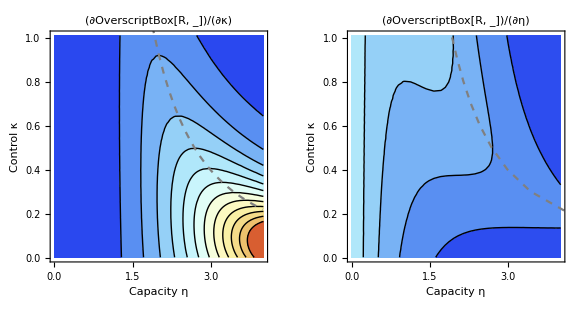

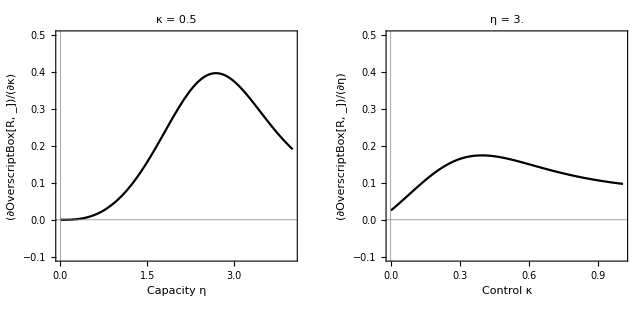

```mathematica
(* run cell above to produce plots *)
(* slice domain *)
ηmin=0.001;ηmax=4.01;
κmin=0.001;κmax=1.01;


(* slice location *)
κsliceat=0.50;
ηsliceat=3.00;



(* find max value of derivative to set contours *)
ηgrid=Subdivide[ηmin,ηmax,100];
κgrid=Subdivide[κmin,κmax,100];

vals1=Flatten@Table[N@dRdκ[η,κ,1.0],{η,ηgrid},{κ,κgrid}];
vals2=Flatten@Table[N@dRdη[η,κ,1.0],{η,ηgrid},{κ,κgrid}];


vals1=Select[vals1,NumericQ];
vals2=Select[vals2,NumericQ];


minVal=Min[Join[vals1,vals2]];
maxVal=Max[Join[vals1,vals2]];

(* style *)
cf=ColorData["LightTemperatureMap"];
cfFixed=(cf[Rescale[#,{minVal,maxVal}]]&);
nContours=12;
tstyle=Directive[Black,12,FontFamily->"Times New Roman"];


(* contour plots for each derivative *)
p1=ContourPlot[dRdκ[η,κ,1.0],{η,ηmin,ηmax},{κ,κmin,κmax},Method->{"TransparentPolygonMesh"->True},PlotTheme->"Scientific",BaseStyle->tstyle,FrameLabel->{Style["Capacity η",tstyle],Style["Control κ",tstyle]},ColorFunctionScaling->False,ColorFunction->cfFixed,Contours->nContours,ContourStyle->Black,ContourShading->True,GridLines->None,PlotRangePadding->0,FrameStyle->Black,FrameTicksStyle->tstyle,PlotLegends->None,PlotLabel->Style["(∂OverscriptBox[R, _])/(∂κ)",tstyle],PlotRange->{{0,ηmax},{0,κmax},{minVal,maxVal}}];


p2=ContourPlot[dRdη[η,κ,1.0],{η,ηmin,ηmax},{κ,κmin,κmax},Method->{"TransparentPolygonMesh"->True},PlotTheme->"Scientific",BaseStyle->tstyle,FrameLabel->{Style["Capacity η",tstyle],Style["Control κ",tstyle]},ColorFunctionScaling->False,ColorFunction->cfFixed,Contours->nContours,ContourStyle->Black,ContourShading->True,GridLines->None,PlotRangePadding->0,FrameStyle->Black,FrameTicksStyle->tstyle,PlotLegends->None,PlotLabel->Style["(∂OverscriptBox[R, _])/(∂η)",tstyle],PlotRange->{{0,ηmax},{0,κmax},{minVal,maxVal}}];

(* max *)
Table[{η,NArgMax[dRdη[η,κ,1.0],{κ,κmin,κmax}]},{η,Range[ηmin,ηmax,.1]}];
p1max =ListLinePlot[%,PlotStyle->{Gray,Dashed},PlotTheme->"Scientific",FrameLabel->{Style["Capacity η",12],Style["Control κ",12]}, PlotRange->{{0,4.1},{0,2.1}}, GridLines->None,PlotRangePadding->0,FrameStyle->Black,GridLinesStyle->Gray ,AspectRatio->1];


Table[{NArgMax[dRdκ[η,κ,1.0],{η,ηmin,ηmax}],κ},{κ,Range[κmin,κmax,.1]}];
p2max=ListLinePlot[%,PlotStyle->{Gray,Dashed},PlotTheme->"Scientific",FrameLabel->{Style["Capacity η",12],Style["Control κ",12]}, PlotRange->{{0,4.1},{0,2.1}}, GridLines->None,PlotRangePadding->0,FrameStyle->Black,GridLinesStyle->Gray ,AspectRatio->1];


legend=BarLegend[{cf,{minVal,maxVal}},LabelStyle->tstyle,LegendLabel->Style["Derivative value",tstyle]];
contoursWithLegend=Legended[GraphicsRow[{Show[{p1,p1max}],Show[{p2,p2max}]},Spacings->Scaled[.10],ImageSize->Large],Placed[legend,Right]]



(* slice plots *)
p3=Plot[dRdκ[η,κsliceat,1.0],{η,ηmin,ηmax},PlotTheme->"Scientific",BaseStyle->tstyle,FrameLabel->{Style["Capacity η",tstyle],Style["(∂OverscriptBox[R, _])/(∂κ)",tstyle]},AspectRatio->1,PlotStyle->Black,PlotRange->{{0.,Automatic},{-.1,.5}},PlotRangePadding->0,FrameStyle->Black,FrameTicksStyle->tstyle,GridLines->{{0},{0}},GridLinesStyle->Gray,PlotLabel->Style[Row[{"κ = ",κsliceat}],tstyle]];



p4=Plot[dRdη[ηsliceat,κ,1.0],{κ,κmin,κmax},PlotTheme->"Scientific",BaseStyle->tstyle,FrameLabel->{Style["Control κ",tstyle],Style["(∂OverscriptBox[R, _])/(∂η)",tstyle]},AspectRatio->1,PlotStyle->Black,PlotRange->{{0.,Automatic},{-.1,.5}},PlotRangePadding->0,FrameStyle->Black,FrameTicksStyle->tstyle,GridLines->{{0},{0}},GridLinesStyle->Gray,PlotLabel->Style[Row[{"η = ",ηsliceat}],tstyle]];

GraphicsRow[{p3,p4}]
```

4. Capacity and control versus metabolic benefit (capacity-control regime plot)

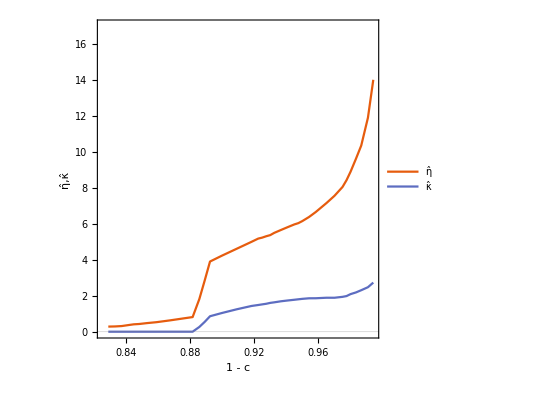

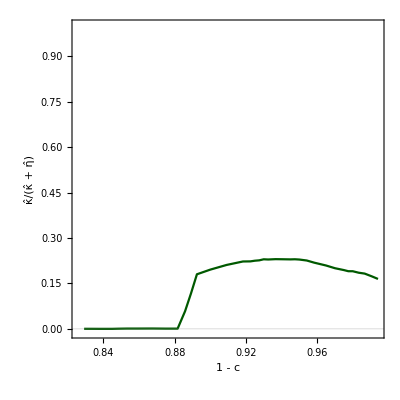

```mathematica
(* set file location *)
file="C: ... Dataset S2.csv";

mVal=4;       (* 2 4 *)
qVal=1.00;    (* 0.75 1.00 *)
TVal=3.0;     (* 2.0 3.0 *)

w=3;        (* moving-average smoothing window, must be odd number *)

(* load *)
raw=Import[file,"CSV"];
headers=ToLowerCase/@ToString/@First@raw;
rows=Rest@raw;
assoc=AssociationThread[headers->#]&/@rows;

(* filter *)
rowsSel=Select[assoc,Round[#["m"]]==mVal&&#["q"]==qVal&&#["t"]==TVal&];

(* aggregate by c *)
byC=GroupBy[rowsSel,#["c"]&];
etaPairs=SortBy[KeyValueMap[{1-#1,Mean[#2[[All,"eta_opt"]]]}&,byC],First];
kappaPairs=SortBy[KeyValueMap[{1-#1,Mean[#2[[All,"kappa_opt"]]]}&,byC],First];
sharePairs=SortBy[KeyValueMap[Function[{cval,r},With[{e=r[[All,"eta_opt"]],k=r[[All,"kappa_opt"]]},{1-cval,Mean@DeleteCases[MapThread[If[#1+#2==0,Nothing,#2/(#1+#2)]&,{e,k}],Nothing]}]],byC],First];

(* smoothing *)
maPairs[p_List,ww_Integer?OddQ]:=If[Length[p]<ww||ww==1,p,Transpose@{MovingAverage[p[[All,1]],ww],MovingAverage[p[[All,2]],ww]}];

etaXY=maPairs[etaPairs,w];
kappaXY=maPairs[kappaPairs,w];
shareXY=maPairs[sharePairs,w];

(* plot *)
baseStyle=Directive[FontFamily->"Times New Roman",FontSize->12];

pltCapCtrl=ListLinePlot[{etaXY,kappaXY},PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["1 - c",12],Style["η̂,κ̂",12]},PlotRange->{All,{-0.01,17}},AspectRatio->1,PlotLegends->Placed[{"η̂","κ̂"},{0.82,0.85}],BaseStyle->baseStyle,ImagePadding->40];

pltShare=ListLinePlot[shareXY,PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["1 - c",12],Style["κ̂/(κ̂ + η̂)",12]},PlotRange->{All,{-0.01,1}},AspectRatio->1,PlotStyle->DarkGreen,BaseStyle->baseStyle,ImagePadding->40];

pltCapCtrl
pltShare
```

5. Information-processing capability and cognitive noise plot

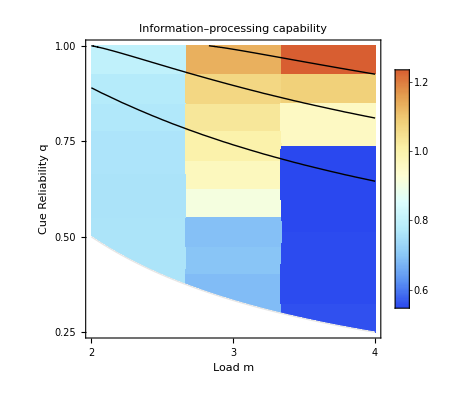

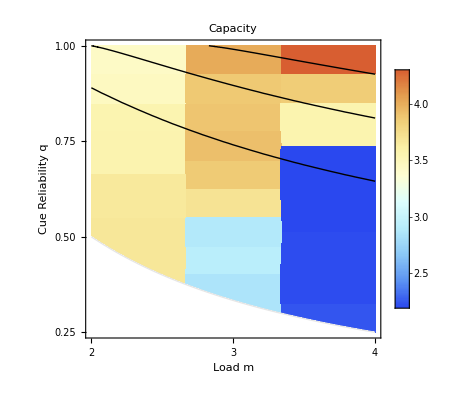

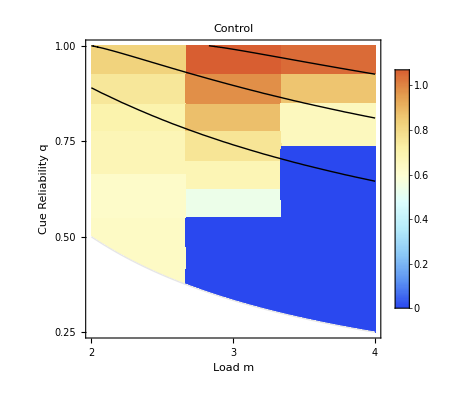

```mathematica
ClearAll["Global`*"];

(* file path including Dataset SX.csv *)
filePath="C:...Dataset S3.csv";

(*choose a slice to visualize*)
cval=0.100;      (* Dataset S1 = {0.10, 0.11, 0.12}, Dataset S3 = {0.095, 0.100, 0.105, 0.110, 0.115, 0.120} *)
Tval=3.0;        (* Dataset S1 = {1, 2, 3} , Dataset S3 = {3} *)

(* load *)
varsToShow={"info_proc_cap","eta_opt","kappa_opt"};
titleMap=<|"info_proc_cap"->"Information–processing capability","eta_opt"->"Capacity","kappa_opt"->"Control"|>;

(* cue information contours *)
i[m_,q_]:=q*Log[2,m*q]+(1-q)*Log[2,m*(1-q)/(m-1)];

tickStyle[n_]:=Style[n,Black,FontFamily->"Times New Roman"];

bottomTicks={{2,tickStyle["2"]},{3,tickStyle["3"]},{4,tickStyle["4"]}};
fmtTop[x_]:=Style[ToString@NumberForm[N[Log[2,x],10],{Infinity,2}],Black,FontFamily->"Times New Roman"];

topTicks={{2,fmtTop[2]},{3,fmtTop[3]},{4,fmtTop[4]}};
qTicks={{0.25,tickStyle["0.25"]},{0.50,tickStyle["0.50"]},{0.75,tickStyle["0.75"]},{1.00,tickStyle["1.00"]}};

infoContours=ContourPlot[i[m,q],{m,2,4},{q,0.25,1},RegionFunction->Function[{m,q,z},q>=1/m],Contours->{0.5,1,1.5},ContourShading->False,PlotRange->{0,2},PlotRangePadding->None,ContourStyle->{Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Black]},Axes->False,Frame->False,FrameTicks->None,BaseStyle->{FontFamily->"Times New Roman",FontColor->Black}];

feasibleBoundary=Plot[1/m,{m,2,4},PlotStyle->{Directive[Thick,GrayLevel[.9]]},Axes->False,Frame->False,PlotRangePadding->None,BaseStyle->{FontFamily->"Times New Roman",FontColor->Black}];

(* load *)
raw=Import[filePath,"CSV"];
headers=ToString/@First@raw;
rows=Rest@raw;

numberStringQ[s_]:=StringQ[s]&&Quiet@Check[NumberQ@ToExpression[s],False];
toNum[x_]:=If[numberStringQ[x],ToExpression[x],x];

data=Map[AssociationThread[headers,toNum/@#]&,rows];

required={"m","q","T","c","eta_opt","kappa_opt","R_bar","info_proc_cap"};
missing=Complement[required,Keys@First@data];
If[missing=!={},Print@Style["Missing columns: "<>StringRiffle[missing,", "],14,Black,FontFamily->"Times New Roman"];
Abort[]];

(* heatmap *)
makeBandHeatmap[sub_,var_,varBounds_]:=Module[{mVals,qVals,mMin,mMax,qMin,qMax,nM,nQ,xC,yC,mMap,qMap,plotData},mVals=Sort@DeleteDuplicates@Lookup[sub,"m",{}];
qVals=Sort@DeleteDuplicates@Lookup[sub,"q",{}];
{mMin,mMax}={First@mVals,Last@mVals};
{qMin,qMax}={First@qVals,Last@qVals};
nM=Length@mVals;nQ=Length@qVals;
(*cell centers for nearest-neighbour look*)xC=Table[mMin+(i-0.5) (mMax-mMin)/nM,{i,nM}];
yC=Table[qMin+(j-0.5) (qMax-qMin)/nQ,{j,nQ}];
mMap=AssociationThread[mVals->xC];
qMap=AssociationThread[qVals->yC];
plotData={mMap[#["m"]],qMap[#["q"]],#[var]}&/@sub;
ListDensityPlot[plotData,InterpolationOrder->0,PlotRange->{{mMin,mMax},{qMin,qMax},varBounds},ColorFunction->"LightTemperatureMap",Frame->False,Axes->False,PlotRangePadding->None,PlotLegends->BarLegend[{"LightTemperatureMap",varBounds},LabelStyle->Directive[Black,FontFamily->"Times New Roman"]],AspectRatio->1,BaseStyle->{FontFamily->"Times New Roman",FontColor->Black}]];

makeWhiteRegion[sub_]:=Module[{mVals,qVals,mMin,mMax,qMin,qMax},mVals=Sort@DeleteDuplicates@Lookup[sub,"m",{}];
qVals=Sort@DeleteDuplicates@Lookup[sub,"q",{}];
{mMin,mMax}={First@mVals,Last@mVals};
{qMin,qMax}={First@qVals,Last@qVals};
RegionPlot[q<1/m&&mMin<=m<=mMax&&qMin<=q<=qMax,{m,mMin,mMax},{q,qMin,qMax},PlotStyle->White,BoundaryStyle->None,Axes->False,Frame->False,PlotRange->All,PlotRangePadding->None,BaseStyle->{FontFamily->"Times New Roman",FontColor->Black}]];

leftLabel=Row[{Style["Cue Reliability ",Black,FontFamily->"Times New Roman"],Style[TraditionalForm[q],Black,Italic,FontFamily->"Times New Roman"]}];
bottomLabel=Row[{Style["Load ",Black,FontFamily->"Times New Roman"],Style[TraditionalForm[m],Black,Italic,FontFamily->"Times New Roman"]}];
topLabel=Row[{Style["Environmental Complexity ",Black,FontFamily->"Times New Roman"],Style[TraditionalForm[H[m]],Black,Italic,FontFamily->"Times New Roman"]}];

(* plotting *)
overlayForVar[Ttarget_,cTarget_,var_]:=Module[{subset,vMin,vMax,vBounds,hm,mask},subset=Select[data,(#["T"]==Ttarget&&#["c"]==cTarget)&];
If[subset==={},Return@Style["No rows match these T and c.",14,Black,FontFamily->"Times New Roman"]];
vMin=Min@Lookup[subset,var];
vMax=Max@Lookup[subset,var];
vBounds={vMin,vMax};
hm=makeBandHeatmap[subset,var,vBounds];
mask=makeWhiteRegion[subset];
Show[hm,mask,infoContours,feasibleBoundary,PlotRange->All,PlotRangePadding->None,Frame->True,FrameStyle->Black,FrameLabel->{{leftLabel,None},{bottomLabel,topLabel}},FrameTicks->{{qTicks,None},{bottomTicks,topTicks}},PlotLabel->Style[titleMap[var],14,Bold,Black,FontFamily->"Times New Roman"],BaseStyle->{FontFamily->"Times New Roman",FontColor->Black}]];

Do[Print@overlayForVar[Tval,cval,v],{v,varsToShow}];
```

```mathematica
|
```